# Unit Box

info@cafeplanck.com

```mathematica
UnitBox[x]//TraditionalForm
```

x

```mathematica
PiecewiseExpand[UnitBox[x]]
```

Piecewise[{{1, -1/2≤x≤1/2}, {0, True}}]

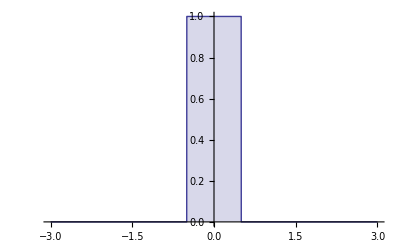

```mathematica
Plot[UnitBox[x],{x,-3,3},Filling->Axis]
```

```mathematica
UnitBox[x,y]//TraditionalForm
```

x,y

```mathematica
PiecewiseExpand[UnitBox[x,y],-3<x<3,-3<y<3]
```

Piecewise[{{1, -1/2≤x≤1/2&&-1/2≤y≤1/2}, {0, True}}]

```mathematica
Plot3D[UnitBox[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
∫_(-∞)^(+∞) UnitBox[x]ⅆx
```

1

```mathematica
FourierTransform[UnitBox[x],x,t]
```

Sinc[t/2]/(√(2 π))

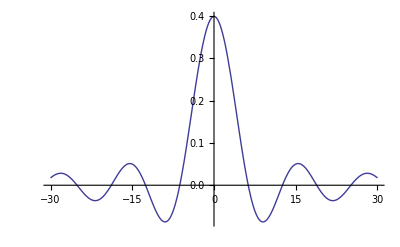

```mathematica
Plot[FourierTransform[UnitBox[x],x,t],{t,-30,30},PlotRange->All]
```